## Rossler System

```mathematica
Clear[a,b,c]
f[{x_,y_,z_}]:={-y-z, x +a y,b+z (x  - c)}
Df[{x_,y_,z_}]=D[f[{x,y,z}],{{x,y,z}}];
MatrixForm[Df[{x,y,z}]]
```

(0 | -1 | -1
1 | a | 0
z | 0 | -c+x)

Numerical solution with standard parameters.

```mathematica
y0=10RandomReal[{-1,1},3];

TMax=123;
{a,b,c}={0.2,0.2,14};
{ySol,JSol}=NDSolveValue[{
y'[t]==f[y[t]],y[0]==y0,
J'[t]==Df[y[t]].J[t],
J[0]==IdentityMatrix[3]
}, {y,J}, {t, 0 ,TMax}];
```

### Basic Plots

```mathematica
ParametricPlot3D[ySol[t],{t,0, TMax},PlotRange->All,PlotPoints->10^3]
```

-Graphics3D-

### Sensitivity Plot

```mathematica
TabView[{
"plain"->Plot[SingularValueList[JSol[t]],{t, 0, TMax},PlotRange->All],
"log"->LogPlot[SingularValueList[JSol[t]],{t, 0, TMax},PlotRange->All]
}]
```

12

### Changing the Parameters

Numerical solution with different parameters. Looks like it joins back up again!

```mathematica
y0=10RandomReal[{-1,1},3];
TMax=223;
{a,b,c}={0.1,0.2,14};
{ySol,JSol}=NDSolveValue[{
y'[t]==f[y[t]],y[0]==y0,
J'[t]==Df[y[t]].J[t],
J[0]==IdentityMatrix[3]
}, {y,J}, {t, 0 ,TMax}];
```

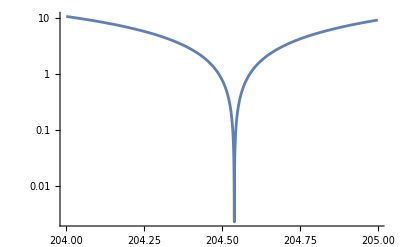

```mathematica
LogPlot[Norm[ySol[t]-ySol[TMax]],{t,204, 205},
PlotRange->All]
```

```mathematica
ySol[TMax]
```

{10.3198,-18.4639,0.0326902}

```mathematica
TMax
```

223

```mathematica
,
PlotRange
```

```mathematica
TabView[{
"3D"->ParametricPlot3D[ySol[t],{t,0.9TMax, TMax},PlotRange->All,PlotPoints->10^3,AxesLabel->{"x","y","z"}],
"x,y,z"->Plot[ySol[t],{t,0.9 TMax, TMax},AxesLabel->{"","t"}],
"log z"->LogPlot[ySol[t]⟦3⟧,{t,0.9 TMax, TMax},AxesLabel->{"z","t"},PlotRange->All]
}]
```

123